## Load packages

### Add notebook directory to package path

```mathematica
AppendTo[$Path,NotebookDirectory[]]
```

{C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\DocumentationIndices,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Kernel,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Autoload,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\Ohdraw.niL,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Packages,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Autoload,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Applications,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Mathematica\14.0\Documentation\English\System,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Data\ICC,C:\Program Files\Wolfram Research\Mathematica\14.0\Documentation\ChineseSimplified\System\,D:\Ohdraw.niL\OneDrive\Programming\Mathematica\packages_custom,D:\Ohdraw.niL\OneDrive\Programming\Julia\Modules\mathematica_nbs\}

### Initialize

```mathematica
SetDirectory[NotebookDirectory[]<>"/.."];
```

```mathematica
<<PlotMatexFormatting`;
```

```mathematica
<<ExtFileLoading`;
```

```mathematica
<<ArrayManip`;
```

```mathematica
<<FileNamings`;
```

```mathematica
<<StrIOManip`;
```

```mathematica
<<FileSaving`;
```

```mathematica
<<MCLoops`;
```

```mathematica
<<Geo3d`;
```

### Reload external evaluators

```mathematica
<<"ExternalEvaluatorLoad.wl"
```

```mathematica
(*<<"ExternalEvaluateJulia`"*)
```

### Check directory

```mathematica
Directory[]
```

D:\Ohdraw.niL\OneDrive\Programming\Julia\Modules

### Check path

```mathematica
$Path
```

{C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\DocumentationIndices,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Kernel,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Autoload,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\Ohdraw.niL,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Packages,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Autoload,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Applications,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Mathematica\14.0\Documentation\English\System,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Data\ICC,C:\Program Files\Wolfram Research\Mathematica\14.0\Documentation\ChineseSimplified\System\,D:\Ohdraw.niL\OneDrive\Programming\Mathematica\packages_custom,D:\Ohdraw.niL\OneDrive\Programming\Julia\Modules\mathematica_nbs\}

## File name constants

### Reading

```mathematica
dirLog="./log/";
```

```mathematica
dirFigs="./figs/";
```

```mathematica
dirFigsDoc="./figs/figsDoc/";
```

```mathematica
fNameFLstLstJld2="fNameFileLstJld2Lst.txt";
fNameFLstLst="fNameFileLstLst.txt";
fNameSaveParamLstLst="fNameSaveParamsLst.txt";
```

```mathematica
fNameFLstWL="fNameFileLstWL.txt";
```

```mathematica
numDigs=3;
```

### Saving

```mathematica
fNameFigLstTmp="fNameFigLstTmp.txt";
```

## Plotting options

```mathematica
pltOptLstNoStyle={BaseStyle->texStyle,Frame->True,PlotRange->All,PlotRangePadding->{None,Automatic}};
```

```mathematica
pltOptLst={BaseStyle->texStyle,Frame->True,ImageSize->8cm,PlotStyle->lineStyleLstDataThick,PlotRange->All,PlotRangePadding->{None,Automatic}};
```

```mathematica
pltOptMatPlot={BaseStyle->texStyle,Frame->True,PlotRangePadding->None};
```

```mathematica
markerStyleLstTmp=markerStyleLstFunc[colorLst,AbsolutePointSize[4]];
```

```mathematica
markerStyleLstLine=markerStyleLstFunc[colorLst,AbsolutePointSize[2]];
```

```mathematica
markerStyleLstOpac=markerStyleLstFunc[Opacity[0.3,#]&/@colorLst,AbsolutePointSize[3]];
```

## Wang Landau density of state plot

```mathematica
fNameWL=readTxtLastLine[dirLog<>fNameFLstWL];
```

```mathematica
fNameWL
```

loops_WL_single_div_4_it_409600_nDim_3_histStdRatioThres_0.15_histCutoff_0.5_wlResetIntrvl_1000_BinomialInit_0.047.jld2

```mathematica
fNameWL="loops_WL_staggered_divNum_4.0_itNum_409600.0_histDivNum_16.0_cAreaInit_3.0_dosIncrInit_2.0.jld2";
```

```mathematica
fNameWLSingle="loops_WL.jld2";
```

```mathematica
histArrFlat=readJuliaVarDimRev[fNameWL,"histArr"];
dosArrFlat=readJuliaVarDimRev[fNameWL,"dosArr"];
```

```mathematica
histArr=readJuliaVarDimRev[fNameWL,"histArr"];
dosArr=readJuliaVarDimRev[fNameWL,"dosArr"];
histDivNum=Length[histArr];
```

```mathematica
dosArr⟦-1⟧
```

718.563

```mathematica
Total[dosArr]
```

13492.8

```mathematica
Total[dosArr]
```

36599.3

```mathematica
histArr
```

{2710,3015,2787,3035,2995,3108,3181,3244,3147,3033,2936,2962,2919,2815,2898,2912,2861,2754,2866,2755,2844,2722,2702,2742,2735,2837,2847,2728,2468,2484,2399,2465,2384,2362,2292,2266,1833,1818,1747,1592,1526,1464,1479,1377,1334,1386,1305,1313,1171,1178,1177,1150,1090,1158,1067,1052,1041,924,907,899,913,977,1014,1011,993,939,933,922,881,869,878,835,846,835,867,921,881,916,909,905,938,947,995,1006,1012,1044,1042,1054,1021,1074,1071,1012,988,987,966,964,986,996,1033,1049,1043,1017,1010,1006,1003,984,969,988,975,969,953,910,903,917,901,878,891,863,874,892,873,931,919,957,941,999,1015,1012,956,963,965,978,970,1000,1015,1015,1022,1015,975,940,960,970,973,931,958,957,927,969,1029,1031,1016,1015,1014,1017,1001,1016,1051,1095,1080,1124,1154,1168,1175,1151,1164,1212,1271,1265,1261,1328,1286,1318,1319,1318,1338,1385,1355,1439,1472,1532,1572,1542,1520,1516,1531,1559,1525,1533,1537,1565,1568,1531,1543,1579,1550,1533,1488,1475,1460,1436,1383,1475,1440,1416,1464,1501,1561,1760,1752,1818,1787,1841,1789,1899,1915,1953,2047,2222,2328,2537,2593,2546,2681,2812,2903,3139,3087,3216,3145,3258,3305,3223,3218,3139,3205,3166,3142,3145,3005,3009,3024,3005,2951,3061,2949,3008,3002,2983,3057,3017,3067,3129,2982,2997,3301}

```mathematica
dosArrFlatSymm=(dosArrFlat+Reverse[dosArrFlat])/2;
```

```mathematica
dosArrSymm=(dosArr+Reverse[dosArr])/2
```

{569.178,573.755,574.355,577.201,578.565,580.827,582.336,584.288,585.828,587.633,589.199,590.938,592.575,594.112,595.678,597.185,598.745,600.198,601.607,602.937,604.121,605.329,606.486,607.467,608.316,609.075,609.753,610.286,610.728,611.111,611.317,611.388,611.317,611.111,610.728,610.286,609.753,609.075,608.316,607.467,606.486,605.329,604.121,602.937,601.607,600.198,598.745,597.185,595.678,594.112,592.575,590.938,589.199,587.633,585.828,584.288,582.336,580.827,578.565,577.201,574.355,573.755,569.178}

```mathematica
dosArr
```

{550.,570.188,561.188,573.625,575.625,581.5,587.438,590.5,593.75,595.688,598.375,603.875,607.688,609.25,611.5,613.438,619.625,626.,629.375,631.563,633.125,638.438,640.875,640.563,645.938,647.375,650.313,652.75,653.938,657.375,659.563,660.063,661.25,664.313,665.625,666.75,669.125,671.25,674.063,674.813,676.875,678.875,680.688,684.813,688.,690.625,695.188,697.563,699.813,701.313,703.875,705.063,708.,710.625,711.938,713.625,715.938,719.438,720.5,723.,723.875,725.75,726.75,727.875,731.375,733.75,735.75,736.625,738.688,739.75,741.438,742.625,744.438,745.375,747.75,748.625,749.5,750.438,751.438,753.938,755.5,759.125,760.063,761.75,762.625,763.375,764.375,766.313,767.563,768.875,770.875,771.625,773.,773.438,774.188,774.875,776.438,778.5,778.625,779.625,780.625,781.938,782.875,784.,784.938,784.75,785.,785.313,785.688,786.375,787.188,787.25,787.875,788.063,788.688,788.438,789.375,789.938,789.688,789.813,790.063,790.438,790.375,790.688,790.188,789.813,790.063,790.25,790.25,790.563,790.563,790.563,790.313,790.063,790.188,789.313,789.563,789.125,788.813,788.688,788.563,788.625,788.563,788.625,788.125,787.813,787.375,786.75,786.313,786.188,785.125,784.375,783.438,782.5,781.625,780.25,778.875,778.75,778.5,778.125,777.188,776.375,775.625,774.563,773.813,771.313,770.125,768.75,767.625,766.438,766.125,763.25,761.125,759.75,757.188,755.5,753.625,753.25,751.125,749.,747.563,745.438,744.25,742.625,741.,739.625,737.5,734.313,732.313,731.563,729.125,724.813,722.938,720.5,719.313,715.875,712.313,710.563,709.25,707.563,706.25,705.313,702.5,701.313,697.313,696.188,691.688,689.75,688.625,687.125,683.5,682.,679.813,677.5,674.875,669.438,666.188,658.938,657.375,653.75,651.813,648.688,646.938,644.5,641.5,638.375,634.938,632.188,631.313,628.,626.375,623.875,623.063,619.188,616.188,613.813,611.,606.375,603.313,602.438,601.75,600.5,597.438,596.25,593.188,588.,581.25,578.375,569.25,560.063,552.375,555.625,547.688,552.,500.688}

```mathematica
dosArr
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,14.,43.,70.,100.,106.,130.,154.,221.,237.,234.,293.,343.,334.,344.,351.,382.,383.,382.,396.,404.,410.,413.,418.,422.,422.,457.,463.,487.,496.,496.,517.,568.,571.,599.,650.,645.,651.,662.,697.,709.,737.,774.,777.,773.,788.,789.,802.,805.,834.,832.,839.,858.,877.,888.,885.,906.,931.,936.,940.,945.,948.,995.,1014.,1021.,1023.,1035.,1037.,1035.,1037.,1041.,1045.,1045.,1052.,1061.,1065.,1068.,1071.,1068.,1073.,1073.,1092.,1095.,1097.,1101.,1106.,1111.,1113.,1116.,1117.,1123.,1136.,1138.,1139.,1138.,1134.,1138.,1140.,1142.,1141.,1149.,1150.,1153.,1155.,1158.,1158.,1156.,1158.,1173.,1170.,1169.,1169.,1168.,1162.,1161.,1162.,1160.,1163.,1162.,1164.,1164.,1164.,1166.,1168.,1169.,1163.,1159.,1152.,1155.,1148.,1148.,1149.,1141.,1144.,1135.,1133.,1127.,1120.,1123.,1121.,1121.,1119.,1117.,1112.,1110.,1110.,1105.,1105.,1097.,1100.,1098.,1098.,1084.,1082.,1080.,1081.,1079.,1073.,1070.,1067.,1057.,1033.,1023.,995.,996.,990.,985.,982.,964.,960.,950.,950.,944.,940.,938.,930.,928.,924.,915.,915.,914.,907.,886.,882.,881.,878.,871.,873.,864.,860.,860.,856.,852.,848.,845.,826.,822.,812.,790.,769.,765.,763.,762.,734.,730.,726.,726.,714.,716.,714.,701.,698.,680.,679.,673.,661.,604.,613.,595.,555.,522.,519.,500.,482.,466.,455.,451.,443.,429.,395.,396.,367.,347.,305.,270.,267.,155.,91.,43.,49.,33.,0.,0.,0.,0.,0.}

```mathematica
dosArr⟦1⟧
```

0.

```mathematica
dosArrNormed=dosArr-Min[dosArr⟦{1,-1}⟧]+Log[2];
```

```mathematica
dosArrFlatSymmNormed=dosArrFlatSymm-Min[dosArrFlatSymm⟦{1,-1}⟧]+Log[2];
```

```mathematica
dosArrSymmNormed=dosArrSymm-Min[dosArrSymm⟦{1,-1}⟧]+Log[2];
```

```mathematica
divNum=8;
```

```mathematica
isingELst={-2 divNum^2}~Join~Range[-2 divNum^2+8,2 divNum^2-8,4]~Join~{2 divNum^2};
```

```mathematica
isingELstFull=Range[-2 divNum^2,2 divNum^2,4];
```

```mathematica
{isingELstNormed,isingELstFullNormed}={isingELst,isingELstFull}/(divNum^2);
```

```mathematica
isingELst
```

{-512,-504,-500,-496,-492,-488,-484,-480,-476,-472,-468,-464,-460,-456,-452,-448,-444,-440,-436,-432,-428,-424,-420,-416,-412,-408,-404,-400,-396,-392,-388,-384,-380,-376,-372,-368,-364,-360,-356,-352,-348,-344,-340,-336,-332,-328,-324,-320,-316,-312,-308,-304,-300,-296,-292,-288,-284,-280,-276,-272,-268,-264,-260,-256,-252,-248,-244,-240,-236,-232,-228,-224,-220,-216,-212,-208,-204,-200,-196,-192,-188,-184,-180,-176,-172,-168,-164,-160,-156,-152,-148,-144,-140,-136,-132,-128,-124,-120,-116,-112,-108,-104,-100,-96,-92,-88,-84,-80,-76,-72,-68,-64,-60,-56,-52,-48,-44,-40,-36,-32,-28,-24,-20,-16,-12,-8,-4,0,4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172,176,180,184,188,192,196,200,204,208,212,216,220,224,228,232,236,240,244,248,252,256,260,264,268,272,276,280,284,288,292,296,300,304,308,312,316,320,324,328,332,336,340,344,348,352,356,360,364,368,372,376,380,384,388,392,396,400,404,408,412,416,420,424,428,432,436,440,444,448,452,456,460,464,468,472,476,480,484,488,492,496,500,504,512}

```mathematica
isingELst=Delete[isingELst,2];
isingELst=Delete[isingELst,-2];
```

Delete::partw: Part {-2} of Delete[{-32,-24,-20,-16,-12,-8,-4,0,4,8,«6»}] does not exist.

```mathematica
divNum^2
```

1024

```mathematica
dosArr⟦1⟧
```

76.25

```mathematica
dosArrNormed⟦1⟧
```

0.693147

```mathematica
xyLabsWL=matexLstFunc[{"E/2L^2","\\log g \\left( E \\right)"},labMag];
```

```mathematica
xyLabsWL
```

{-Graphics-,-Graphics-}

```mathematica
legLstWLExact=matexLstFunc[{"\\mathrm{Wang\\, Landau}","\\mathrm{exact}"},labMag];
```

```mathematica
titleWL16=MaTeX["16 \\times 16 \\, , \\, 3.2 \\times 10^6 \\mathrm{\\, iterations}",Magnification->labMag];
```

```mathematica
dosArrSymmNormed//Dimensions
```

{63}

```mathematica
isingELstNormed//Dimensions
```

{63}

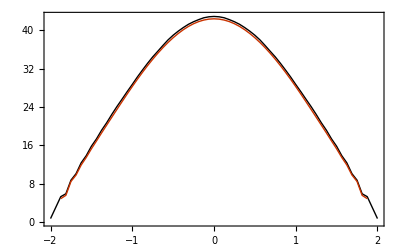

```mathematica
pltWL16Exact=ListLinePlot[{{isingELstNormed,dosArrSymmNormed}ᵀ,{isingELstFullNormed,gExactLst8}ᵀ},pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick,Axes->False,FrameLabel->xyLabsWL,PlotLegends->Placed[LineLegend[legLstWLExact,Spacings->0.3],Scaled[{0.5,0.5}]],PlotLabel->titleWL16]
```

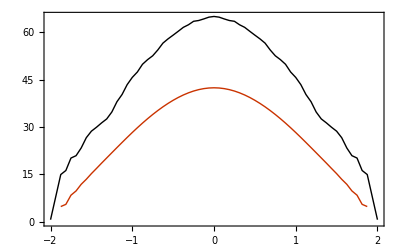

```mathematica
pltWL16Exact=ListLinePlot[{{isingELstNormed,dosArrSymmNormed}ᵀ,{isingELstFullNormed,gExactLst8}ᵀ},pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick,Axes->False,FrameLabel->xyLabsWL,PlotLegends->Placed[LineLegend[legLstWLExact,Spacings->0.3],Scaled[{0.5,0.5}]],PlotLabel->titleWL16]
```

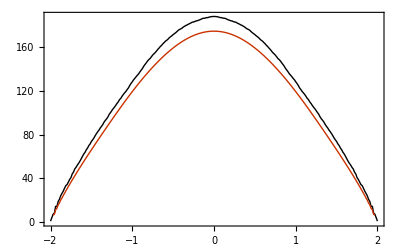

```mathematica
pltWL16Exact=ListLinePlot[{{isingELstNormed,dosArrSymmNormed}ᵀ,{isingELstFullNormed,gExactLst16}ᵀ},pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick,Axes->False,FrameLabel->xyLabsWL,PlotLegends->Placed[LineLegend[legLstWLExact,Spacings->0.3],Scaled[{0.5,0.5}]],PlotLabel->titleWL16]
```

```mathematica
titleFlatExplored=MaTeX["16 \\times 16 \\mathrm{\, flatness\\, condition\\,comparison}",Magnification->labMag]
```

-Graphics-

```mathematica
legLstWLFlatExplored=matexLstFunc[{"\\mathrm{explored (good)}","\\mathrm{all (bad)}","\\mathrm{exact}"},labMag];
```

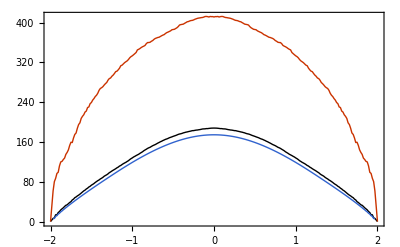

```mathematica
pltWL16FlatCmp=ListLinePlot[{{isingELstNormed,dosArrSymmNormed}ᵀ,{isingELstNormed,dosArrFlatSymmNormed}ᵀ,{isingELstFullNormed,gExactLst16}ᵀ},pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick,Axes->False,FrameLabel->xyLabsWL,PlotLegends->Placed[LineLegend[legLstWLFlatExplored,Spacings->0.3],Scaled[{0.5,0.7}]],PlotLabel->titleFlatExplored]
```

```mathematica
Export[dirFigsDoc<>"WLIsing16FlatCmp.pdf",pltWL16FlatCmp]
```

./figs/figsDoc/WLIsing16FlatCmp.pdf

```mathematica
Export[dirFigsDoc<>"WLIsing16.pdf",pltWL16Exact]
```

./figs/figsDoc/WLIsing16.pdf

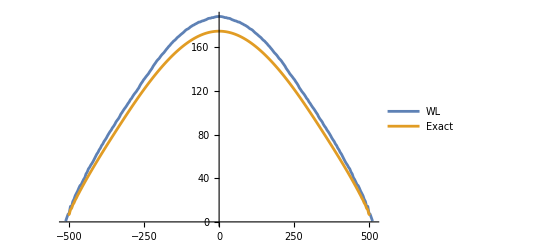

```mathematica
ListLinePlot[{{isingELst,dosArrSymmNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

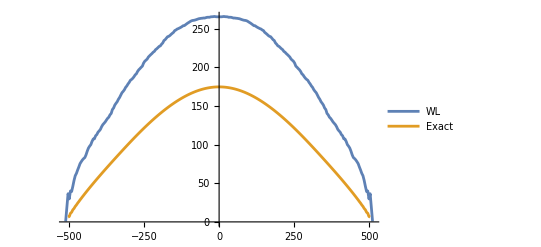

```mathematica
ListLinePlot[{{isingELst,dosArrSymmNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

```mathematica
ListLinePlot[{{isingELst,dosArrSymmNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

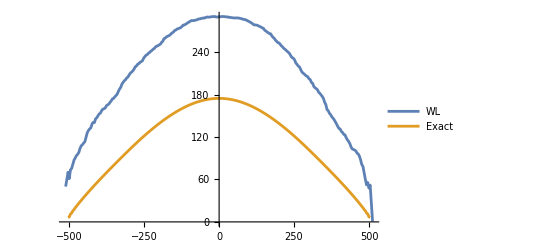

```mathematica
ListLinePlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

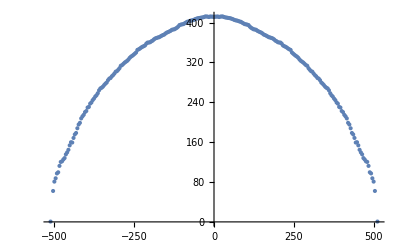

```mathematica
ListPlot[{isingELst,dosArrFlatSymmNormed}ᵀ]
```

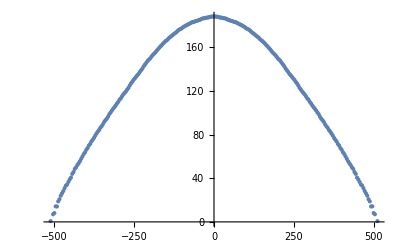

```mathematica
ListPlot[{isingELst,dosArrSymmNormed}ᵀ]
```

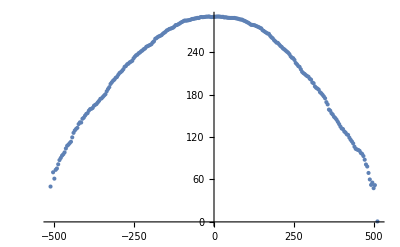

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

-Graphics-

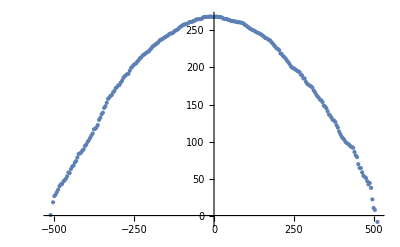

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

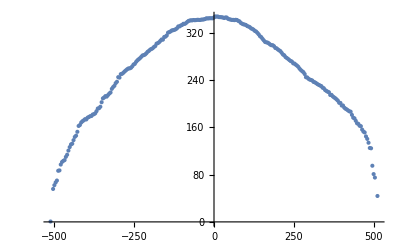

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

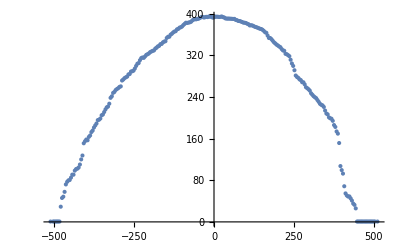

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

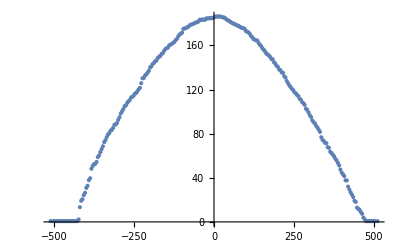

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

-Graphics-

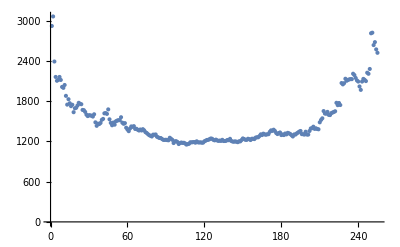

```mathematica
ListPlot[histArr]
```

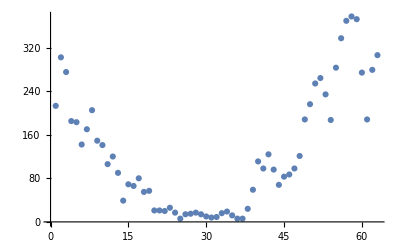

```mathematica
ListPlot[histArr]
```

```mathematica
gExactLst16=gExactLst;
```

```mathematica
gExactLst=splot⟦All,2⟧;
```

```mathematica
gExactLst//Dimensions
```

{37}

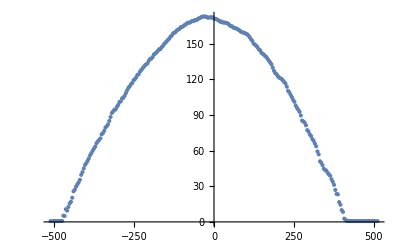

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

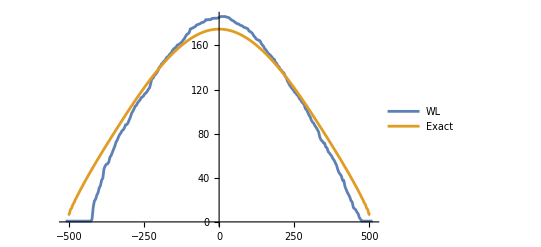

```mathematica
ListLinePlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

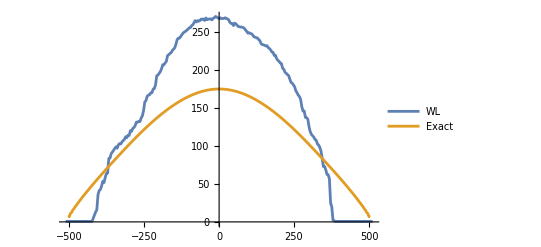

```mathematica
ListLinePlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

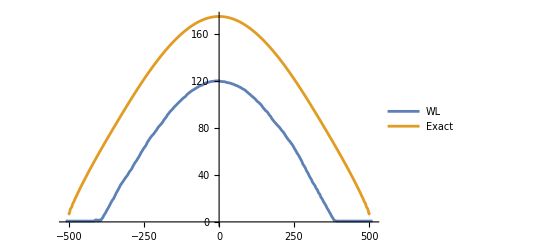

```mathematica
ListLinePlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

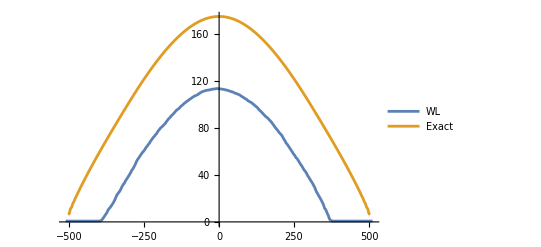

```mathematica
ListLinePlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

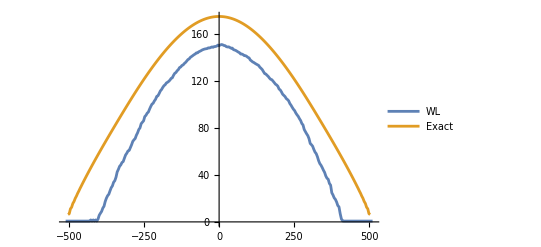

```mathematica
ListLinePlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

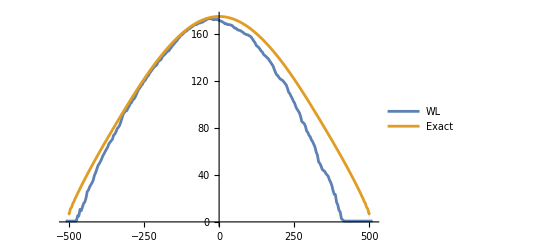

```mathematica
ListLinePlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

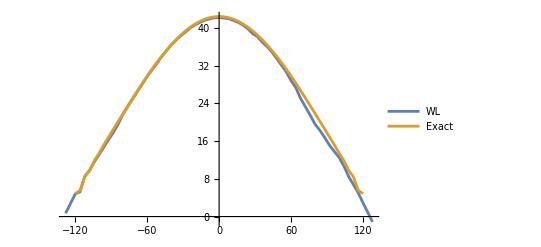

```mathematica
ListLinePlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst8}ᵀ},PlotLegends->{"WL","Exact"}]
```

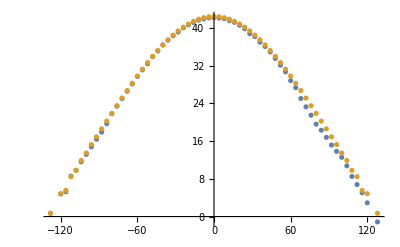

```mathematica
ListPlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst8}ᵀ}]
```

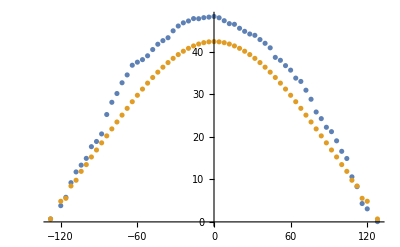

```mathematica
ListPlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst8}ᵀ}]
```

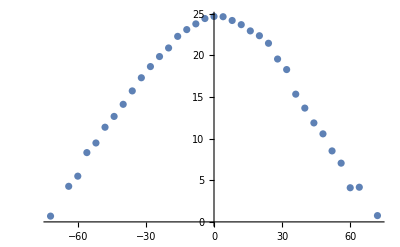

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ,]
```

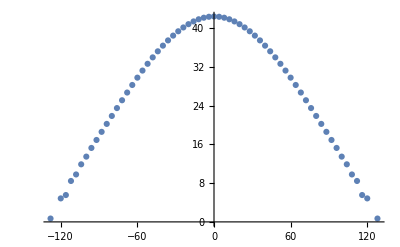

```mathematica
ListPlot[{isingELstFull,gExactLst}ᵀ]
```

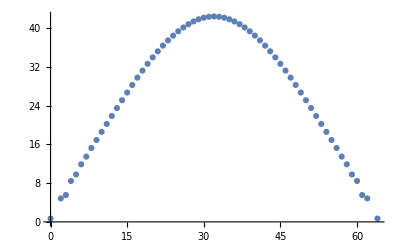

```mathematica
ListPlot[splot]
```

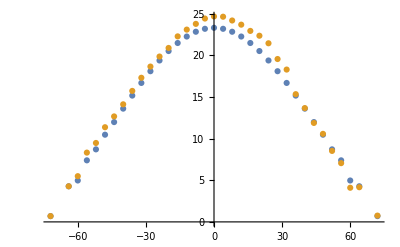

```mathematica
ListPlot[{{isingELstFull,gExactLst}ᵀ,{isingELst,dosArrNormed}ᵀ}]
```

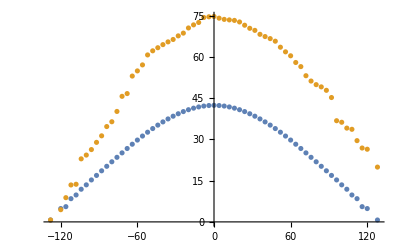

```mathematica
ListPlot[{{isingELstFull,gExactLst}ᵀ,{isingELst,dosArrNormed}ᵀ}]
```

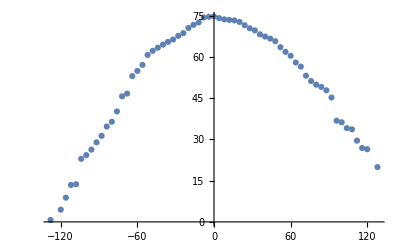

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

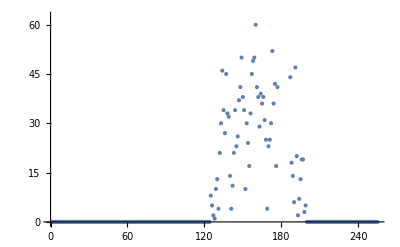

```mathematica
ListPlot[histArr]
```

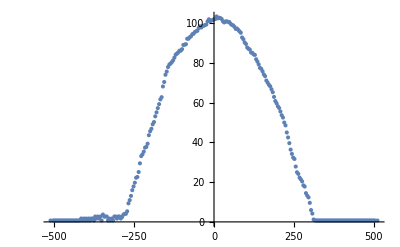

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

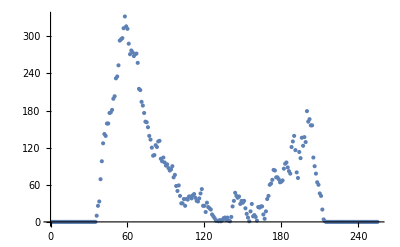

```mathematica
ListPlot[histArr]
```

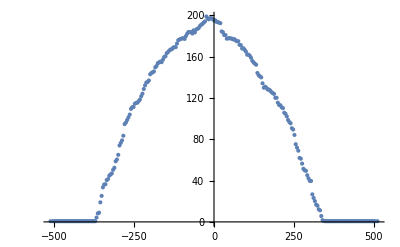

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

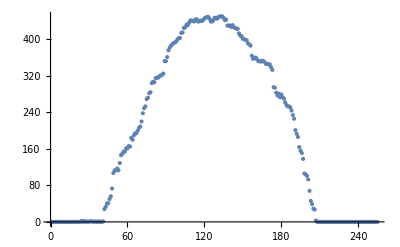

```mathematica
ListPlot[histArr]
```

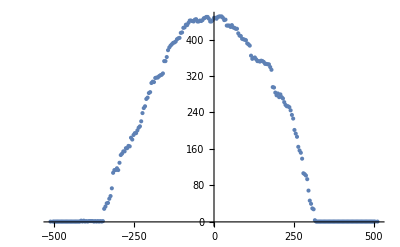

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

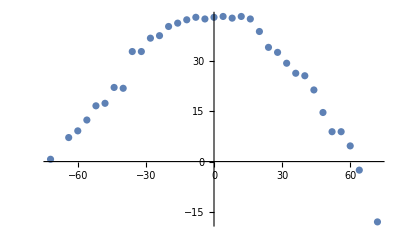

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

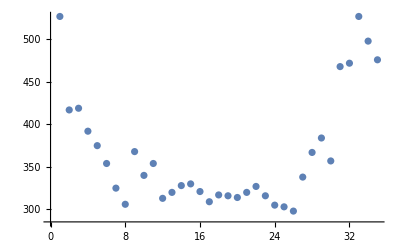

```mathematica
ListPlot[histArr]
```

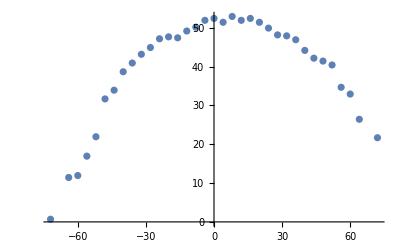

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

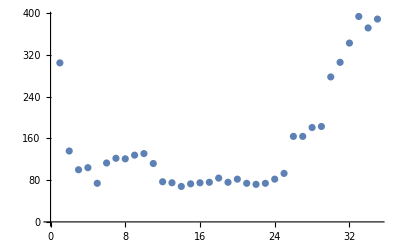

```mathematica
ListPlot[histArr]
```

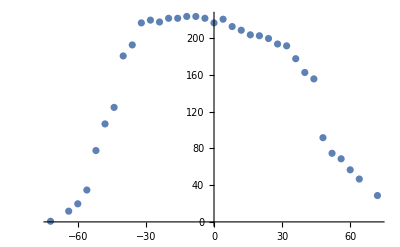

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

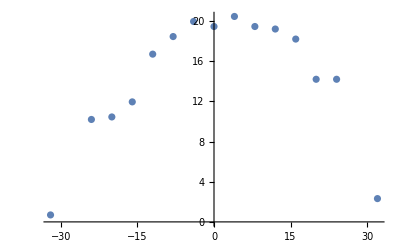

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

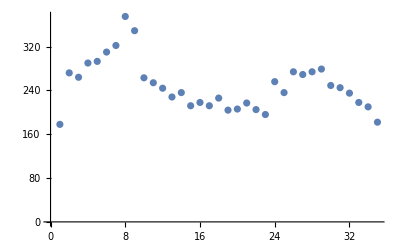

```mathematica
ListPlot[histArr]
```

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

-Graphics-

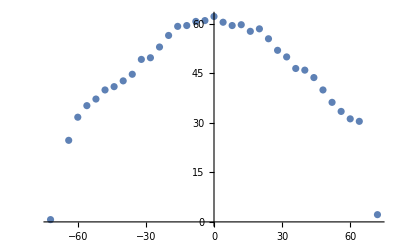

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

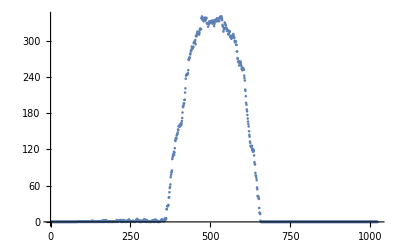

```mathematica
ListPlot[histArr]
```

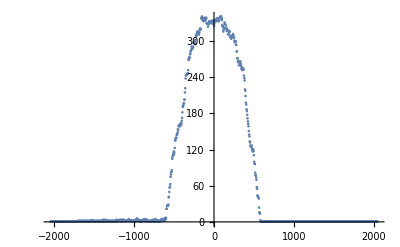

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

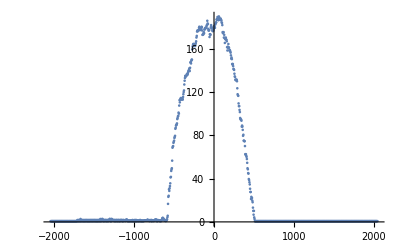

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

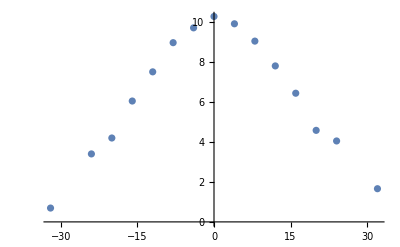

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

```mathematica
Delete[isingELst,-2]
```

{-32,-28,-24,-20,-16,-12,-8,-4,0,4,8,12,16,20,24,32}

```mathematica
dosArr//Dimensions
```

{15}

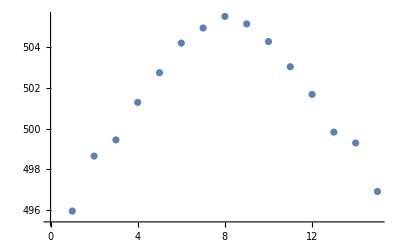

```mathematica
ListPlot[dosArr]
```

```mathematica
histArr=readJuliaVarDimRev[fNameWL,"histArr"];
```

```mathematica
dosArr=readJuliaVarDimRev[fNameWL,"dosArr"];
```

```mathematica
histArrSingle=histArr;
```

```mathematica
fNameSingle="loops_WL_single_divNum_4_itNum_40960000_histDivNum_16_cAreaInit_3_dosIncrInit_2.0.jld2";
```

```mathematica
histArrSingle=readJuliaVarDimRev[fNameSingle,"histArr"];
```

```mathematica
histArrSingle=readJuliaVarDimRev[fNameWLSingle,"histArr"];
```

```mathematica
histArrSingle//Dimensions
```

{80,80}

```mathematica
histDivNum=Length[histArr];
```

```mathematica
histDivNum=Length[histArrSingle];
```

```mathematica
histArr//Dimensions
```

{512,512}

```mathematica
Max[histArrSingle]
```

281

```mathematica
Min[histArrSingle]
```

0

```mathematica
Total[histArrSingle,-1]
```

40960000

```mathematica
Max[{{1,2},{3,4}}]
```

4

```mathematica
Total[histArr,-1]
```

51200

```mathematica
Max[histArr]
```

122

```mathematica
histArr
```

```mathematica
histArrNon0=Map[#>0&,histArrSingle,{2}]/.subBoolIntPlot;
```

```mathematica
histArrNon0//Dimensions
```

{256,256}

```mathematica
256^2
```

65536

```mathematica
Total[histArrNon0,-1]
```

83

```mathematica
Max[histArr]/Total[histArr,-1]//N
```

0.00238281

```mathematica
Max[histArr]/Total[histArr,-1]//N
```

0.00149918

```mathematica
Length[histArrSingle]
```

16

```mathematica
Length[histArrSingle⟦1⟧]
```

16

```mathematica
histArr3d=Table[{ii,jj,histArrSingle⟦ii,jj⟧},{ii,Length[histArrSingle]},{jj,Length[histArrSingle⟦1⟧]}];
```

```mathematica
testArr=histArr⟦2031;;2080,2031;;2080⟧;
```

```mathematica
testArr3d=Table[{ii,jj,testArr⟦ii,jj⟧},{ii,Length[testArr]},{jj,Length[testArr⟦1⟧]}];
```

```mathematica
ListPlot3D[histArr3d]
```

-Graphics3D-

```mathematica
ListPlot3D[testArr]
```

-Graphics3D-

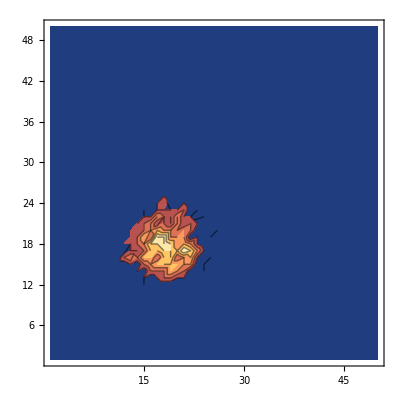

```mathematica
ListContourPlot[testArr]
```

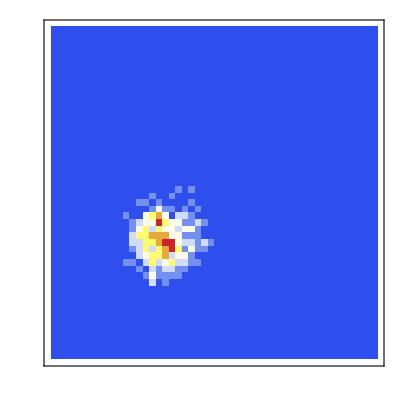

```mathematica
ArrayPlot[Transpose@histArr⟦2031;;2080,2031;;2080⟧,pltOptMatPlot,DataReversed->True,ColorFunction->"TemperatureMap"]
```

```mathematica
ListPlot3D[dosArr⟦1;;100,1;;100⟧,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArr⟦201;;300,201;;300⟧,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[histArr⟦201;;300,201;;300⟧,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[histArr⟦201;;300,201;;300⟧,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[histArr⟦71;;150,71;;150⟧,PlotRange->All]
```

-Graphics3D-

```mathematica
histArr⟦1,1⟧
```

0

```mathematica
ArrayPlot[Transpose@histArr,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
ArrayPlot[Transpose@histArr,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
Total[histArrSing,-1]
```

9809

```mathematica
ArrayPlot[Transpose@histArrSingle,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
ArrayPlot[Transpose@histArrSingle,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
ArrayPlot[Transpose@histArrSingle,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All]
```

-Graphics3D-

```mathematica
ArrayPlot[Transpose@histArrSingle,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All]
```

-Graphics3D-

```mathematica
ArrayPlot[Transpose@histArrSingle,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All]
```

-Graphics3D-

```mathematica
ArrayPlot[Transpose@histArrSingle,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All]
```

-Graphics3D-

```mathematica
ArrayPlot[Transpose@histArrSingle,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
ListPlot3D[histArr,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All,AxesLabel->{"cA","cL","logG"}]
```

-Graphics3D-

```mathematica
ArrayPlot[Transpose@histArrSingle,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
3 4^3
```

192

```mathematica
ListPlot3D[histArr,PlotRange->All,AxesLabel->{"cA","cL","logG"}]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All,AxesLabel->{"cA","cL","logG"}]
```

-Graphics3D-

### Plot3d

```mathematica
histArrCoord=Flatten[Table[({ii-0.5,jj-0.5}/histDivNum)~Join~{histArr⟦ii,jj⟧},{ii,histDivNum},{jj,histDivNum}],1];
dosArrCoord=Flatten[Table[({ii-0.5,jj-0.5}/histDivNum)~Join~{dosArr⟦ii,jj⟧},{ii,histDivNum},{jj,histDivNum}],1];
```

```mathematica
dosArrPartFlatIntrvl1000=dosArr;
```

```mathematica
dosArrPartFlat=dosArr;
dosArrPartFlatCord=dosArrCoord;
```

```mathematica
dosValArrCoord=Flatten[Table[({ii-0.5,jj-0.5}/histDivNum)~Join~{Exp[dosArr⟦ii,jj⟧-Max[dosArr]]},{ii,histDivNum},{jj,histDivNum}],1];
```

```mathematica
histArrCoord//Dimensions
```

{256,3}

```mathematica
histArrCoord⟦1⟧
```

{0.03125,0.03125,0}

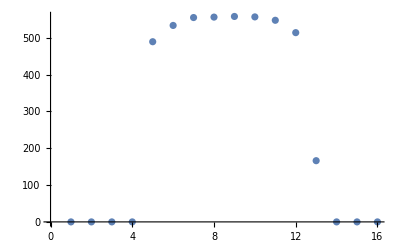

```mathematica
ListPlot[dosArrPartFlat⟦8⟧]
```

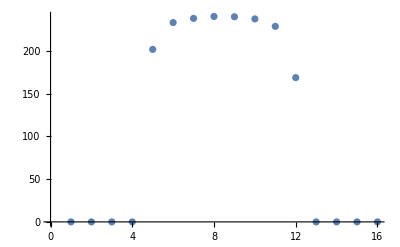

```mathematica
ListPlot[dosArrPartFlatIntrvl1000⟦8⟧]
```

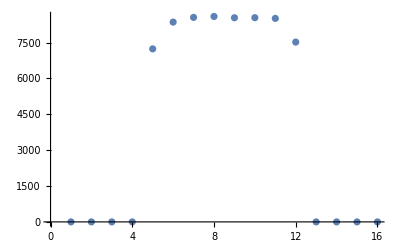

```mathematica
ListPlot[dosArr⟦8⟧]
```

```mathematica
histTitle=MaTeX["H \\left( s, \\ell \\right)",Magnification->labMag];
```

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"S(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"S(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"S(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"S(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"S(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"S(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"S(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"S(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"S(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"S(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"S(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"S(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosValArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"S(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"S(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose@histArrSingle,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

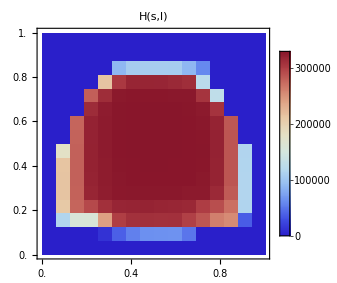

```mathematica
ArrayPlot[Reverse@Transpose@histArrSingle,pltOptMatPlot,ColorFunction->"ThermometerColors",FrameLabel->Reverse[xyLabNoDimLst⟦All,2⟧],DataRange->{{0.5/histDivNum,1-0.5/histDivNum},{0.5/histDivNum,1-0.5/histDivNum}},FrameTicks->{Range[0,1,0.2]},PlotLegends->Automatic,PlotLabel->"H(s,l)",ImageSize->10cm]
```

```mathematica
testArr=ConstantArray[Range[10],10]
```

{{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10}}

```mathematica
ListPlot3D[testArr,AxesLabel->{"x","y","h"}]
```

-Graphics3D-